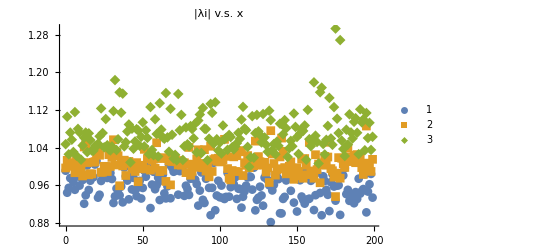

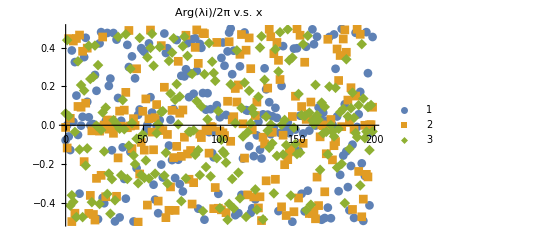

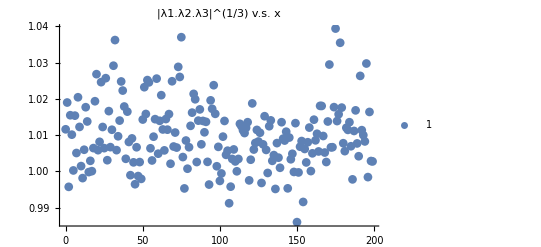

5.67756

-2.24194

-0.103745

3.33187

a1,a2,a3

0.000165188

3.17319

721757.

expection

2.58333

```mathematica
(*modified orthogonal, Ne=10, 0.425 Lx.Ly*)
codbar=Import["Google Drive/jie_programs/QHlattice/berry_matrix_recalculation/output_modified_orthogonal_ne10","Table"];
n:=Length[codbar]
d=Table[codbar[[i]][[1]],{i,1,n,1}];
amp1=Table[{d[[i]],codbar[[i]][[5]]},{i,1,n,3}];
ang1=Table[{d[[i]],codbar[[i]][[6]]/(2π)},{i,1,n,3}];
amp2=Table[{d[[i]],codbar[[i]][[5]]},{i,2,n,3}];
ang2=Table[{d[[i]],codbar[[i]][[6]]/(2π)},{i,2,n,3}];
amp3=Table[{d[[i]],codbar[[i]][[5]]},{i,3,n,3}];
ang3=Table[{d[[i]],codbar[[i]][[6]]/(2π)},{i,3,n,3}];

ListPlot[{amp1,amp2,amp3},PlotLegends->{"1","2","3"},PlotMarkers->Automatic, PlotLabel->"|λi| v.s. x"]
ListPlot[{ang1,ang2,ang3},PlotLegends->{"1","2","3"},PlotMarkers->Automatic, PlotLabel-> "Arg(λi)/2π v.s. x"]
ListPlot[{(amp1*amp2*amp3)^(1/3)},PlotLegends->{"1","2","3"},PlotMarkers->Automatic, PlotLabel->"|λ1.λ2.λ3|^(1/3) v.s. x"]

g1=Sum[ang1[[i]][[2]],{i,1,n/3}]
g2=Sum[ang2[[i]][[2]],{i,1,n/3}]
g3=Sum[ang3[[i]][[2]],{i,1,n/3}]
g1+g2+g3
Print["a1,a2,a3"]
a1=Product[amp1[[i]][[2]],{i,1,n/3}]
a2=Product[amp2[[i]][[2]],{i,1,n/3}]
a3=Product[amp3[[i]][[2]],{i,1,n/3}]
Print["expection"]
31/4/3//N
```

```mathematica
13*0.4*2*π/3
```

10.8909

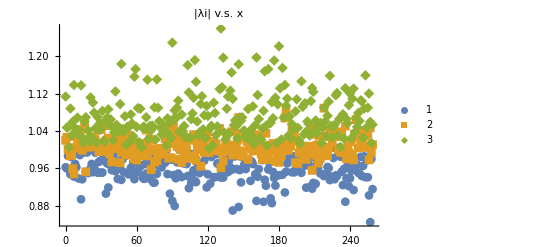

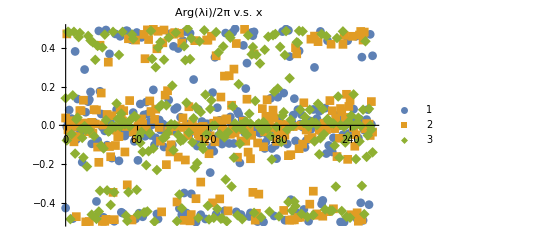

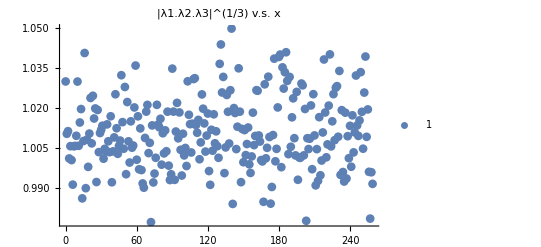

-3.24627

-2.01761

1.15157

-4.11231

a1,a2,a3

0.0000198364

7.5293

3.16215×10^7

expection

1.73333

```mathematica
(*modified orthogonal, Ne=4, 0.4 Lx.Ly*)
codbar=Import["Google Drive/jie_programs/QHlattice/berry_matrix_recalculation/output_modified_orthogonal","Table"];
n:=Length[codbar]
d=Table[codbar[[i]][[1]],{i,1,n,1}];
amp1=Table[{d[[i]],codbar[[i]][[5]]},{i,1,n,3}];
ang1=Table[{d[[i]],codbar[[i]][[6]]/(2π)},{i,1,n,3}];
amp2=Table[{d[[i]],codbar[[i]][[5]]},{i,2,n,3}];
ang2=Table[{d[[i]],codbar[[i]][[6]]/(2π)},{i,2,n,3}];
amp3=Table[{d[[i]],codbar[[i]][[5]]},{i,3,n,3}];
ang3=Table[{d[[i]],codbar[[i]][[6]]/(2π)},{i,3,n,3}];

ListPlot[{amp1,amp2,amp3},PlotLegends->{"1","2","3"},PlotMarkers->Automatic, PlotLabel->"|λi| v.s. x"]
ListPlot[{ang1,ang2,ang3},PlotLegends->{"1","2","3"},PlotMarkers->Automatic, PlotLabel-> "Arg(λi)/2π v.s. x"]
ListPlot[{(amp1*amp2*amp3)^(1/3)},PlotLegends->{"1","2","3"},PlotMarkers->Automatic, PlotLabel->"|λ1.λ2.λ3|^(1/3) v.s. x"]

g1=Sum[ang1[[i]][[2]],{i,1,n/3}]
g2=Sum[ang2[[i]][[2]],{i,1,n/3}]
g3=Sum[ang3[[i]][[2]],{i,1,n/3}]
g1+g2+g3
Print["a1,a2,a3"]
a1=Product[amp1[[i]][[2]],{i,1,n/3}]
a2=Product[amp2[[i]][[2]],{i,1,n/3}]
a3=Product[amp3[[i]][[2]],{i,1,n/3}]
Print["expection"]
13*0.4/3
```

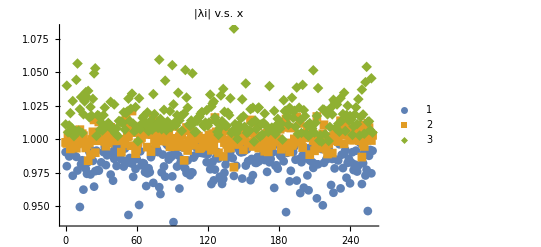

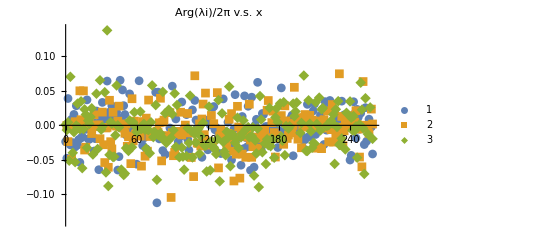

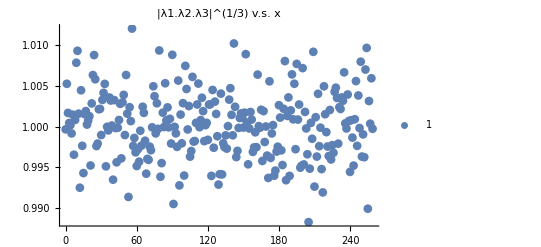

10.3351

2.2507

2.20025

14.786

a1,a2,a3

0.0118418

1.16108

84.892

```mathematica
(*orthogonal, Ne=4, 0.4 Lx.Ly*)
codbar=Import["Google Drive/jie_programs/QHlattice/berry_matrix_recalculation/output_orthogonal","Table"];
n:=Length[codbar]
d=Table[codbar[[i]][[1]],{i,1,n,1}];
amp1=Table[{d[[i]],codbar[[i]][[5]]},{i,1,n,3}];
ang1=Table[{d[[i]],codbar[[i]][[6]]/(2π)},{i,1,n,3}];
amp2=Table[{d[[i]],codbar[[i]][[5]]},{i,2,n,3}];
ang2=Table[{d[[i]],codbar[[i]][[6]]/(2π)},{i,2,n,3}];
amp3=Table[{d[[i]],codbar[[i]][[5]]},{i,3,n,3}];
ang3=Table[{d[[i]],codbar[[i]][[6]]/(2π)},{i,3,n,3}];

ListPlot[{amp1,amp2,amp3},PlotLegends->{"1","2","3"},PlotMarkers->Automatic, PlotLabel->"|λi| v.s. x"]
ListPlot[{ang1,ang2,ang3},PlotLegends->{"1","2","3"},PlotMarkers->Automatic, PlotLabel-> "Arg(λi)/2π v.s. x"]
ListPlot[{(amp1*amp2*amp3)^(1/3)},PlotLegends->{"1","2","3"},PlotMarkers->Automatic, PlotLabel->"|λ1.λ2.λ3|^(1/3) v.s. x"]

g1=Sum[ang1[[i]][[2]],{i,1,n/3}]
g2=Sum[ang2[[i]][[2]],{i,1,n/3}]
g3=Sum[ang3[[i]][[2]],{i,1,n/3}]
g1+g2+g3
Print["a1,a2,a3"]
a1=Product[amp1[[i]][[2]],{i,1,n/3}]
a2=Product[amp2[[i]][[2]],{i,1,n/3}]
a3=Product[amp3[[i]][[2]],{i,1,n/3}]
```

```mathematica
13*0.4
0.8*π*2

13*0.4/3*2*π//N
13*0.4/3//N
```

5.2

5.02655

10.8909

1.73333

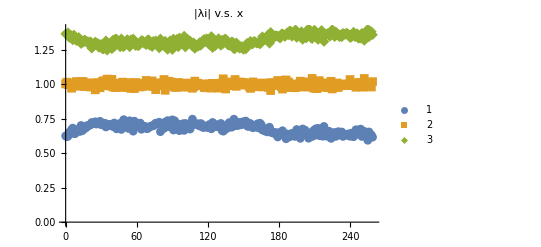

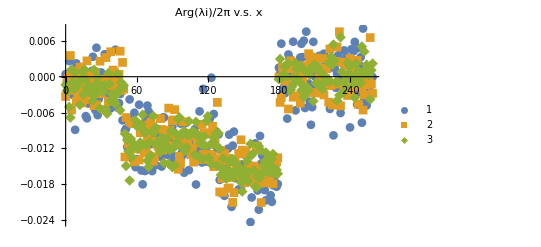

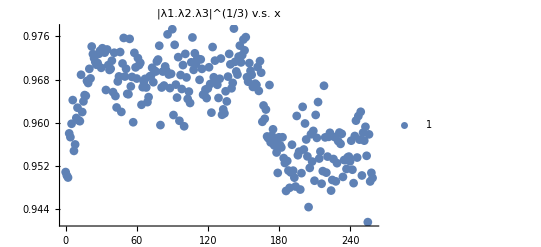

-1.76953

-1.70764

-1.73681

-5.21398

1.73333

5.2

```mathematica
(*nonorthogonal, Ne=4, 0.4 Lx.Ly*)
codbar=Import["Google Drive/jie_programs/QHlattice/berry_matrix_recalculation/output_nonorthogonal_ne4","Table"];
n:=Length[codbar]
d=Table[codbar[[i]][[1]],{i,1,n,1}];
amp1=Table[{d[[i]],codbar[[i]][[5]]},{i,1,n,3}];
ang1=Table[{d[[i]],codbar[[i]][[6]]/(2π)},{i,1,n,3}];
amp2=Table[{d[[i]],codbar[[i]][[5]]},{i,2,n,3}];
ang2=Table[{d[[i]],codbar[[i]][[6]]/(2π)},{i,2,n,3}];
amp3=Table[{d[[i]],codbar[[i]][[5]]},{i,3,n,3}];
ang3=Table[{d[[i]],codbar[[i]][[6]]/(2π)},{i,3,n,3}];

ListPlot[{amp1,amp2,amp3},PlotLegends->{"1","2","3"},PlotMarkers->Automatic, PlotLabel->"|λi| v.s. x"]
ListPlot[{ang1,ang2,ang3},PlotLegends->{"1","2","3"},PlotMarkers->Automatic, PlotLabel-> "Arg(λi)/2π v.s. x"]
ListPlot[{(amp1*amp2*amp3)^(1/3)},PlotLegends->{"1","2","3"},PlotMarkers->Automatic, PlotLabel->"|λ1.λ2.λ3|^(1/3) v.s. x"]

g1=Sum[ang1[[i]][[2]],{i,1,n/3}]
g2=Sum[ang2[[i]][[2]],{i,1,n/3}]
g3=Sum[ang3[[i]][[2]],{i,1,n/3}]
g1+g2+g3

(4*3+1)*0.4/3
(4*3+1)*0.4
```

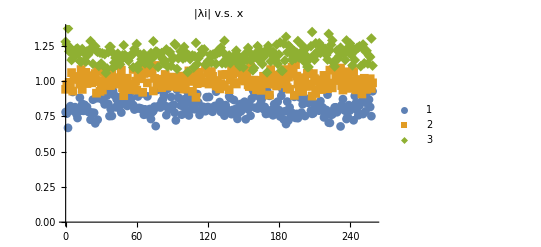

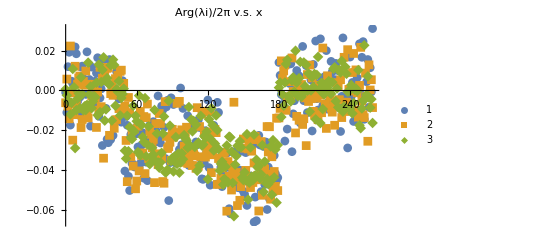

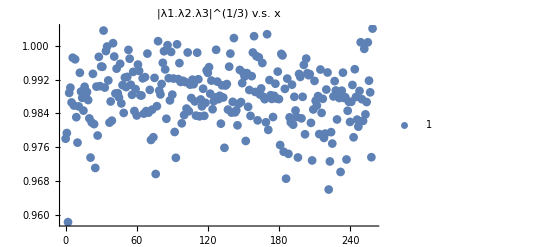

-4.15215

-4.30482

-3.97384

1.1333×10^-23

1.25709

6.10734×10^18

-12.4308

```mathematica
(*nonorthogonal, Ne=10, 0.4 Lx.Ly*)
codbar=Import["Google Drive/jie_programs/QHlattice/berry_matrix_recalculation/output_nonorthogonal_ne10","Table"];
n:=Length[codbar]
d=Table[codbar[[i]][[1]],{i,1,n,1}];
amp1=Table[{d[[i]],codbar[[i]][[5]]},{i,1,n,3}];
ang1=Table[{d[[i]],codbar[[i]][[6]]/(2π)},{i,1,n,3}];
amp2=Table[{d[[i]],codbar[[i]][[5]]},{i,2,n,3}];
ang2=Table[{d[[i]],codbar[[i]][[6]]/(2π)},{i,2,n,3}];
amp3=Table[{d[[i]],codbar[[i]][[5]]},{i,3,n,3}];
ang3=Table[{d[[i]],codbar[[i]][[6]]/(2π)},{i,3,n,3}];

ListPlot[{amp1,amp2,amp3},PlotLegends->{"1","2","3"},PlotMarkers->Automatic, PlotLabel->"|λi| v.s. x"]
ListPlot[{ang1,ang2,ang3},PlotLegends->{"1","2","3"},PlotMarkers->Automatic, PlotLabel-> "Arg(λi)/2π v.s. x"]
ListPlot[{(amp1*amp2*amp3)^(1/3)},PlotLegends->{"1","2","3"},PlotMarkers->Automatic, PlotLabel->"|λ1.λ2.λ3|^(1/3) v.s. x"]

g1=Sum[ang1[[i]][[2]],{i,1,n/3}]
g2=Sum[ang2[[i]][[2]],{i,1,n/3}]
g3=Sum[ang3[[i]][[2]],{i,1,n/3}]
a1=Product[amp1[[i]][[2]],{i,1,n/3}]
a2=Product[amp2[[i]][[2]],{i,1,n/3}]
a3=Product[amp3[[i]][[2]],{i,1,n/3}]
g1+g2+g3
```

```mathematica
(10*3+1)*0.4/3
```

4.13333

```mathematica
0.133*2*π
```

0.835664

```mathematica
31/4/3//N
```

2.58333